# ICARUS TEST Spectrum Code

ICARUS - Inverse Compton Scattering Semi-Analytical Recoil -Corrected Ultra-Relativistic Spectrum Code
• Parallel processing code designed to run on apsv2 DL server
• Generates head-on point source spectra from Gaussian electron bunch and laser pulse distributions. Takes into account energy spread of electron bunch and laser pulse, emittance in 2D and polarisation.
• Based on the work of C. Sun [PRSTAB 14, 044701 (2011)], “Flew too close to C. Sun, Got burnt”. Parallel processing, feasible laser mode calculation and correction to spectral yield imposed.
• Sun’s Thesis: Characterizations and Diagnostics of Compton Light Source is a better description of this model.
• Benchmarked against ICCS3D by Balsa Terzic + Geoff Krafft, with strong agreement, almost identical.

Code History
An extension of the SUN1D (Eγ vs dNγ/dEγ ) to SUN2D. Previously in SUN1D (16) PRSTAB 12, 062801 (2009) the vertical emittance effect is neglected, as storage ring beams are used. ERL’s can use Non-round beams at IP (and these are optimal) so a 2D calculation is required, this is also needed to benchmark an improvement (relating to when source size and collimator size are similar) to ICCS3D by Balsa Terzic. The 2D model uses (3.18) of C. Sun’s thesis (also found in (A8) PRSTAB 14, 044701 (2011)). Code has subsequently been upgraded to ICARUS, utilizing high performance computing.

Potential Error Sources
• The integral over k goes from ∞ to 0 to sum over all modes (confirmed by Geoff) in the laser but its impractical. Implemented k ± 3Δk to just go for the fundamental harmonic + a bandwidth. Convergence tested successfully.
• Terms such as N_laser and z_R which are outside the integration are actually dependent on λ and therefore k. I can understand N_Laser as it is taking the average and it is invariant but z_R seems more spurious. z_R is held constant throughout currently. (Geoff says taking these as constant is the best approximation we can do).
• Currently the code does not take the laser bandwidth variation into account with the cross section, whilst this is predicted to be a small effect it is still not a full treatment of laser energy spread. In practice this means that EL is kept constant during integration. Maybe this full treatment could be added though? - It is a very small effect.
• Point source approximation only holds for far-field collimation.

## Units, Constants and Simulation Setup

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
mJ=10^-3;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
cm=10^-2;
μm=10^-6;
```

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Plot Units*)
phkeVnC=(keV*nC)/elecharge;
phMeVnC=(MeV*nC)/elecharge;
```

## Cases

```mathematica
CBETA150RMS={Ee->150MeV,Q->32pC,Epulse->62μJ,λ->1064nm,θcol->0.43333mrad,ϕ->0,ϵnx->0.3mm mrad,βx->0.126176,ϵny->0.3mm mrad,βy->0.126176,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"keV"};
CBETA150FWHM={Ee->150MeV,Q->32pC,Epulse->62μJ,λ->1064nm,θcol->0.256mrad,ϕ->0,ϵnx->0.3mm mrad,βx->0.269211,ϵny->0.3mm mrad,βy->0.269211,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->100,range->"keV"};
CBETA150Baseline={Ee->150MeV,Q->32pC,Epulse->62μJ,λ->1064nm,θcol->0.5mrad,ϕ->0,ϵnx->0.3mm mrad,βx->0.01,ϵny->0.3mm mrad,βy->0.01,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->100,range->"keV"};

DIANA340={Ee->340MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.18848mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.3592,ϵny->0.5mm mrad,βy->0.3592,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA680={Ee->680MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.09461mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.7181,ϵny->0.5mm mrad,βy->0.7181,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1020={Ee->1020MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol0->0.06328mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.0756,ϵny->0.5mm mrad,βy->1.0756,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};

NEQSRNRF1={Ee->245.58MeV,Q->1nC,Epulse->100μJ,λ->532nm,θcol->0.239mrad,ϕ->0,ϵnx->1mm mrad,βx->0.3459,ϵny->1mm mrad,βy->0.3459,σL->25μm,ΔEe->8.6*10^-4,Δk->5*10^-4,L->10,npts->70,range->"MeV"};
NEQSRNRF2={Ee->245.58MeV,Q->1nC,Epulse->100μJ,λ->656nm,θcol->0.239mrad,ϕ->0,ϵnx->1mm mrad,βx->0.3459,ϵny->1mm mrad,βy->0.3459,σL->25μm,ΔEe->8.6*10^-4,Δk->5*10^-4,L->10,npts->70,range->"MeV"};

CLS300NdYAG={Ee->99.71MeV,Q->200pC,Epulse->100μJ,λ->1064nm,θcol->0.873mrad,ϕ->0,ϵnx->1mm mrad,βx->7.49cm,ϵny->1mm mrad,βy->7.49cm,σL->25μm,tpulse->5ps,ΔEe->8.6*10^-4,Δk->6.5*10^-4,L->10,npts->70,range->"keV"};
CLS300HoYAG={Ee->99.71MeV,Q->200pC,Epulse->100μJ,λ->2120nm,θcol->0.873mrad,ϕ->0,ϵnx->1mm mrad,βx->7.49cm,ϵny->1mm mrad,βy->7.49cm,σL->25μm,tpulse->5ps,ΔEe->8.6*10^-4,Δk->6.5*10^-4,L->10,npts->70,range->"keV"};

(*DIANA Latest Configurations: Subscript[E, inj] = 7 MeV, Subscript[E, Acc] = 15, 22.24 MV/m, Fundamental Harmonic*) 
DIANA347RMS={Ee->347MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.18848mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.3592,ϵny->0.5mm mrad,βy->0.3592,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA687RMS={Ee->687MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.09461mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.7181,ϵny->0.5mm mrad,βy->0.7181,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA687FWHM={Ee->687MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.055mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.606699,ϵny->0.5mm mrad,βy->1.606699,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1027RMS={Ee->1027MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.06328mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.0756,ϵny->0.5mm mrad,βy->1.0756,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};

DIANA511={Ee->511MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.12567mrad,ϕ->0,ϵnx->0.5mm mrad,βx->0.5396473415644379,ϵny->0.5mm mrad,βy->0.5396473415644379,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1015={Ee->1015MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.06359mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.0706237174466873,ϵny->0.5mm mrad,βy->1.0706237174466873,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};
DIANA1519={Ee->1519MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.04269mrad,ϕ->0,ϵnx->0.5mm mrad,βx->1.6003780693786585,ϵny->0.5mm mrad,βy->1.6003780693786585,σL->25μm,ΔEe->5*10^-4,Δk->6.57*10^-4,L->10,npts->70,range->"MeV"};

DIANA1072RMS={Ee->1072MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.061mrad,ϕ->0,ϵnx->0.5mm mrad,βx->3.90,ϵny->0.5mm mrad,βy->0.874,σL->25μm,ΔEe->5*10^-5,Δk->6.57*10^-4,L->10,npts->100,range->"MeV"};
```

Currently envisioned experimental run of the FEBE ICS source for 1k photons collimated. Using Q = 10 pC @ 0.28 mrad.  Inflated electron bunch energy spread to 0.1% for ease of simulation.

```mathematica
FEBE250RMS={Ee->250MeV,Q->10pC,Epulse->0.1,λ->800nm,θcol->0.28mrad,ϕ->0,ϵnx->5mm mrad,βx->0.24512,ϵny->5mm mrad,βy->0.24512,σL->45μm,ΔEe->5*10^-4,Δk->0.03185,L->10,npts->400,range->"MeV"};

FEBE250CASEB={Ee->250MeV,Q->10pC,Epulse->0.1,λ->800nm,θcol->0.221mrad,ϕ->0,ϵnx->1.0mm mrad,βx->1.23,ϵny->1.0mm mrad,βy->1.23,σL->45μm,ΔEe->8*10^-5,Δk->0.03185,L->10,npts->70,range->"MeV"};
FEBE250CASEC={Ee->250MeV,Q->10pC,Epulse->60mJ,λ->1064nm,θcol->0.249mrad,ϕ->0,ϵnx->1.0mm mrad,βx->1.23,ϵny->1.0mm mrad,βy->1.23,σL->45μm,ΔEe->8*10^-5,Δk->1*10^-4,L->10,npts->70,range->"MeV"};
```

Optimisation and Characterisation Spectra
• Use the GA NRB optimised settings for the cases 100M QMC

```mathematica
CaseA={Ee->1000MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.0659233mrad,ϕ->0,ϵnx->0.5mm mrad,βx->2.112,ϵny->0.5mm mrad,βy->0.866691,σL->30μm,ΔEe->10^-4,Δk->4.66*10^-4,L->10,npts->100,range->"MeV"};
CaseB={Ee->700MeV,Q->3000pC,Epulse->100μJ,λ->1064nm,θcol->0.194386mrad,ϕ->0,ϵnx->18.78mm mrad,βx->11.0505,ϵny->0.233mm mrad,βy->0.200543,σL->30μm,ΔEe->6.07*10^-4,Δk->4.66*10^-4,L->10,npts->100,range->"MeV"};
CaseC={Ee->25MeV,Q->10pC,Epulse->100μJ,λ->1064nm,θcol->2.62523mrad,ϕ->0,ϵnx->0.1mm mrad,βx->0.0293893,ϵny->0.1mm mrad,βy->0.0125441,σL->30μm,ΔEe->3*10^-4,Δk->4.66*10^-4,L->10,npts->100,range->"keV"};
CaseClower={Ee->(25MeV-me),Q->10pC,Epulse->100μJ,λ->1064nm,θcol->2.62523mrad,ϕ->0,ϵnx->0.1mm mrad,βx->0.0293893,ϵny->0.1mm mrad,βy->0.0125441,σL->30μm,ΔEe->3*10^-4,Δk->4.66*10^-4,L->10,npts->150,range->"keV"};
```

npts determines the no. points used to produce the spectrum, range states whether you want a keV or MeV units system, Ee is the kinetic energy of the electron beam. Δk is the laser wavenumber spread (just laser energy spread as proportional).

```mathematica
CaseAψ={Ee->1000MeV,Q->100pC,Epulse->100μJ,λ->1064nm,θcol->0.4085903707495668mrad,ϕ->0,ϵnx->0.5mm mrad,βx->3.53,ϵny->0.5mm mrad,βy->3.53,σL->30μm,ΔEe->10^-4,Δk->4.66*10^-4,L->10,npts->100,range->"MeV"};
```

```mathematica
CaseBψ={Ee->700MeV,Q->3000pC,Epulse->100μJ,λ->1064nm,θcol->0.194386mrad,ϕ->0,ϵnx->18.78mm mrad,βx->11.0505,ϵny->0.233mm mrad,βy->0.200543,σL->30μm,ΔEe->6.07*10^-4,Δk->4.66*10^-4,L->10,npts->100,range->"MeV"};
```

## Simulation Setup

```mathematica
NKERNEL=20;
NQMC=(*100*10^6;*)100*10^6;
rmsBW=(13/.81)/100;
```

```mathematica
trialcase=CaseClower;
```

## Polarisation

Polarisation should not affect the no. photons produced by an ICS source and will not affect this in terms of the polar angle (or scattered photon energy). Polarisation only causes an azimuthal angle variation in the spectrum. Therefore, any polarisation can be set yielding an identical spectrum. This part of Sun’s model needed re-casting so the azimuthal scattering plane angle was in terms of the polar scattering angles - the cylindrical to cartesian transformation wasn’t performed properly, but is fixed now.

```mathematica
(*τ=0;
ϕf=0;*)
τ=0;
ϕf[θx_,θy_]:=ArcCos[θx/Sqrt[θx^2+θy^2]];
Pt=1;
Pc=0;
```

## Scattered Photon Energy Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ;(*in eV, hbar is in eV, 2π due to hbar*)
```

EL is the energy of the incident photon in eV. EL is independent of k, this is currently used for the “averaged” values of N_L and z_R and also used in the “averaged” cross section terms.

## Scattered Photon Energy

```mathematica
Eγset[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
Eγset[λ,Ee,ϕ,θcol]/.trialcase
```

10968.2

## Sun Preliminaries

```mathematica
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(EL[λ]*elecharge);
ϵx[Ee_,ϵnx_]:=ϵnx/(β[Ee]*γ[Ee]);
ϵy[Ee_,ϵny_]:=ϵny/(β[Ee]*γ[Ee]);
zr[λ_,σL_]:=(4*π*σL^2)/λ;
σe[ΔEe_,Ee_]:=ΔEe*Ee;
klaser[λ_]:=(2π)/λ;
σk[Δk_,λ_]:=Δk*klaser[λ];
```

```mathematica
σelectron[βIP_,Ee_,ϵn_]:=Sqrt[βIP*ϵx[Ee,ϵn]];
```

```mathematica
(σelectron[βy,Ee,ϵny]/.CaseC)/μm
```

5.01314

The σ_k term usage here could be wrong. It is undefined in Sun’s works, it has been assumed to mirror the form used for the electron bunch energy spread.

## Collimation

```mathematica
R[L_,θcol_]:=L*θcol;(*Far field collimation, small angle approximation*)
```

```mathematica
(*Circular Collimation*)
x0[L_,θcol_]:=R[L,θcol];
y0[L_,θcol_,xd_]:=Re[Sqrt[R[L,θcol]^2-xd^2]];
(*Square Collimation*)
(*x0[A_]:=A;
y0[B_]:=B;*)
```

Square aperture created in two dimensions (x_0= A for x_d, y_0=B for x_d), Circular aperture based on the radius (x_0=R for x_d, y_0= Re Sqrt[R^2 - x_d^2] for y_d or vice versa depending on order of integration).  Obviously, comment out whichever you’d not like to use. Circular collimation is better for narrowband ICS sources.

## Sun Intermediaries

Here we assume collisions are done at a waist i.e α_x=α_y= 0. Therefore, the ξ_(x/y) formula are simplified from Sun’s thesis.

```mathematica
γbar[λ_,Eγ_,θx_,θy_]:=(2*Eγ*EL[λ])/(me*(4*EL[λ]-Eγ*(θx^2+θy^2)))*(1+Sqrt[1+((4*EL[λ]-Eγ*(θx^2+θy^2))*me^2)/(4*EL[λ]^2*Eγ)]);
ξx[βx_,L_,k_,Ee_,ϵnx_,λ_,σL_]:=1+(βx/L)^2+(2*k*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ξy[βy_,L_,k_,Ee_,ϵny_,λ_,σL_]:=1+(βy/L)^2+(2*k*βy*ϵy[Ee,ϵny])/zr[λ,σL];
ζx[k_,βx_,Ee_,ϵnx_,λ_,σL_]:=1+(2*k*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζy[k_,βy_,Ee_,ϵny_,λ_,σL_]:=1+(2*k*βy*ϵy[Ee,ϵny])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,k_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,k,Ee,ϵnx,λ,σL])/(βx*ζx[k,βx,Ee,ϵnx,λ,σL])];
σθy[Ee_,ϵny_,βy_,L_,k_,λ_,σL_]:=Sqrt[(ϵy[Ee,ϵny]*ξy[βy,L,k,Ee,ϵny,λ,σL])/(βy*ζy[k,βy,Ee,ϵny,λ,σL])];
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θymax[λ_,Eγ_]:=Sqrt[(4*EL[λ])/Eγ];
θxmax[λ_,Eγ_,θy_]:=Sqrt[(4*EL[λ])/Eγ-θy^2];
```

The limits of integration have both been constructed using EL i.e the constant case.

```mathematica
kmin[λ_,Δk_]:=klaser[λ]*(1-3*Δk);
kmax[λ_,Δk_]:=klaser[λ]*(1+3*Δk);
```

## Prefactor

```mathematica
prefactor[Q_,Epulse_,λ_,σL_,ΔEe_,Ee_,Δk_,L_]:=(re^2*Ne[Q]*NL[Epulse,λ])/(4*π^3*hbar*clight*zr[λ,σL]*σγ[ΔEe,Ee]*σk[Δk,λ]*L^2);
```

```mathematica
prefactor[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L]/.trialcase//ScientificForm
```

2.57939×10^-4

## Separated Integral Terms

```mathematica
term1[k_,βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_]:=1/(Sqrt[ζx[k,βx,Ee,ϵnx,λ,σL]*ζy[k,βy,Ee,ϵny,λ,σL]]*σθx[Ee,ϵnx,βx,L,k,λ,σL]*σθy[Ee,ϵny,βy,L,k,λ,σL]);
```

```mathematica
term2[λ_,Eγ_,θx_,θy_]:=γbar[λ,Eγ,θx,θy]/(1+(2*γbar[λ,Eγ,θx,θy]*EL[λ])/me);
```

```mathematica
term3[λ_,Eγ_,θx_,θy_,τ_]:=(1/4*((4*γbar[λ,Eγ,θx,θy]^2*EL[λ])/(Eγ*(1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2)))+(Eγ*(1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2)))/(4*γbar[λ,Eγ,θx,θy]^2*EL[λ]))-(1+Pt)*Cos[τ-ϕf[θx,θy]]^2*(γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2))/((1+γbar[λ,Eγ,θx,θy]^2*(θx^2+θy^2))^2));
```

```mathematica
term4[θx_,xd_,L_,Ee_,ϵnx_,βx_,k_,λ_,θy_,yd_,ϵny_,βy_,Eγ_,ΔEe_,Δk_,σL_]:=Exp[-(θx-xd/L)^2/(2*σθx[Ee,ϵnx,βx,L,k,λ,σL]^2)-(θy-yd/L)^2/(2*σθy[Ee,ϵny,βy,L,k,λ,σL]^2)-(γbar[λ,Eγ,θx,θy]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)-(k-klaser[λ])^2/(2*σk[Δk,λ]^2)];
```

## Energy Spread Investigation - [INVESTIGATION]

```mathematica
ESPREADinINT[λ_,Eγ_,θx_,θy_,Ee_,ΔEe_]:=1/σγ[ΔEe,Ee]*Exp[-(γbar[λ,Eγ,θx,θy]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)];
```

```mathematica
intESPREAD[λ_,Eγ_,Ee_,ΔEe_]:=NIntegrate[ESPREADinINT[λ,Eγ,θx,θy,Ee,ΔEe]/.trialcase,{θy,-θymax[λ,Eγ]/.trialcase,θymax[λ,Eγ]/.trialcase},{θx,-θxmax[λ,Eγ,θy]/.trialcase,θxmax[λ,Eγ,θy]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->NQMC}];
```

```mathematica
LaunchKernels[NKERNEL];
```

```mathematica
DistributeDefinitions[{MeV,intESPREAD,trialcase,Elow,Ehigh,Estep}];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::maxp]];
```

```mathematica
ESPREADinv=ParallelTable[{Eγ/MeV,intESPREAD[λ,Eγ,Ee,ΔEe]/.trialcase},{Eγ,Elow[rmsBW,λ,Ee,ϕ]/.trialcase,Ehigh[λ,Ee,ΔEe,ϕ]/.trialcase,Estep[λ,Ee,ΔEe,ϕ,rmsBW,npts]/.trialcase}];
```

ParallelTable::iterb: Iterator {Eγ,Elow[0.0377716,1/1250000,250000000,0],Ehigh[1/1250000,250000000,1/1000,0],Estep[1/1250000,250000000,1/1000,0,0.0377716,100]} does not have appropriate bounds.

ParallelTable::nopar1: ParallelTable[{Eγ/MeV,intESPREAD[λ,Eγ,Ee,ΔEe]/.trialcase},{Eγ,Elow[0.0377716,1/1250000,250000000,0],Ehigh[1/1250000,250000000,1/1000,0],Estep[1/1250000,250000000,1/1000,0,0.0377716,100]}] cannot be parallelized; proceeding with sequential evaluation.

Table::iterb: Iterator {Eγ,Elow[0.0377716,1/1250000,250000000,0],Ehigh[1/1250000,250000000,1/1000,0],Estep[1/1250000,250000000,1/1000,0,0.0377716,100]} does not have appropriate bounds.

```mathematica
CloseKernels[];
```

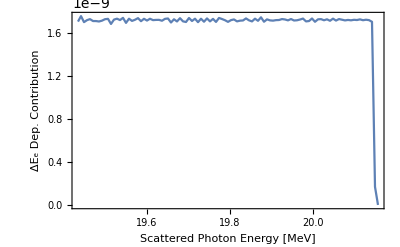

```mathematica
ListLinePlot[ESPREADinv,Frame->True,FrameLabel->{"Scattered Photon Energy [MeV]","ΔE_e Dep. Contribution"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotRange->Full]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/DIANA/EspreadProblem"];
ESPREADinv>>"DIANA1072_RMS_20M_5x10-5.txt";
```

## Integral Term

```mathematica
intterm[k_,βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_,Eγ_,θx_,θy_,τ_,xd_,yd_,ΔEe_,Δk_]:=term1[k,βx,Ee,ϵnx,λ,βy,ϵny,L,σL]*term2[λ,Eγ,θx,θy]*term3[λ,Eγ,θx,θy,τ]*term4[θx,xd,L,Ee,ϵnx,βx,k,λ,θy,yd,ϵny,βy,Eγ,ΔEe,Δk,σL]
```

```mathematica
INTterm[βx_,Ee_,ϵnx_,λ_,βy_,ϵny_,L_,σL_,Eγ_,τ_,ΔEe_,Δk_]:=NIntegrate[intterm[k,βx,Ee,ϵnx,λ,βy,ϵny,L,σL,Eγ,θx,θy,τ,xd,yd,ΔEe,Δk]/.trialcase,{xd,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{yd,-y0[L,θcol,xd]/.trialcase,y0[L,θcol,xd]/.trialcase},{θy,-θymax[λ,Eγ]/.trialcase,θymax[λ,Eγ]/.trialcase},{θx,-θxmax[λ,Eγ,θy]/.trialcase,θxmax[λ,Eγ,θy]/.trialcase},{k,kmin[λ,Δk]/.trialcase,kmax[λ,Δk]/.trialcase},Method->{"QuasiMonteCarlo",MaxPoints->NQMC}];
```

## Energy Range

```mathematica
Elow[rmsBW_,λ_,Ee_,ϕ_]:=(1-3*2*Sqrt[2*Log[2]]*rmsBW)*Eγset[λ,Ee,ϕ,0];
```

```mathematica
Ehigh[λ_,Ee_,ΔEe_,ϕ_]:=Eγset[λ,Ee*(1+5*ΔEe),ϕ,0];
```

```mathematica
Estep[λ_,Ee_,ΔEe_,ϕ_,rmsBW_,npts_]:=(Ehigh[λ,Ee,ΔEe,ϕ]-Elow[rmsBW,λ,Ee,ϕ])/npts;
```

## Spectral Density Calculation

```mathematica
dNdEγ[Q_,Epulse_,λ_,σL_,ΔEe_,Ee_,Δk_,L_,βx_,ϵnx_,βy_,ϵny_,Eγ_,τ_]:=prefactor[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L]*INTterm[βx,Ee,ϵnx,λ,βy,ϵny,L,σL,Eγ,τ,ΔEe,Δk];
```

```mathematica
LaunchKernels[NKERNEL];
```

```mathematica
DistributeDefinitions[{dNdEγ,Which[(range/.trialcase)=="keV",phkeVnC,(range/.trialcase)=="MeV",phMeVnC],Which[(range/.trialcase)=="keV",keV,(range/.trialcase)=="MeV",MeV],Eγset,trialcase,Elow,Ehigh,Estep}];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::maxp]];
```

```mathematica
SpecDen=ParallelTable[{Eγ/Which[(range/.trialcase)=="keV",keV,(range/.trialcase)=="MeV",MeV],Which[(range/.trialcase)=="keV",phkeVnC,(range/.trialcase)=="MeV",phMeVnC]/((Q/.trialcase)/elecharge)*dNdEγ[Q,Epulse,λ,σL,ΔEe,Ee,Δk,L,βx,ϵnx,βy,ϵny,Eγ,τ]/.trialcase},{Eγ,10.8keV(*Elow[rmsBW,λ,Ee,ϕ]/.trialcase*),Ehigh[λ,Ee,ΔEe,ϕ]/.trialcase,(*Estep[λ,Ee,ΔEe,ϕ,rmsBW,npts]/.trialcase*)(Ehigh[λ,Ee,ΔEe,ϕ]-10.8keV)/npts/.trialcase}]//AbsoluteTiming;
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,897,25].

Kernels::rdead: Subkernel connected through KernelObject[16,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {5} assigned to KernelObject[16,local,<defunct>].

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,894,22].

Kernels::rdead: Subkernel connected through KernelObject[13,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {8} assigned to KernelObject[13,local,<defunct>].

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,887,15].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[6,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {15} assigned to KernelObject[6,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[16,local,<defunct>] resurrected as KernelObject[21,local].

LaunchKernels::clone: Kernel KernelObject[13,local,<defunct>] resurrected as KernelObject[22,local].

LaunchKernels::clone: Kernel KernelObject[6,local,<defunct>] resurrected as KernelObject[23,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[242,local,<defunct>] failed.

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[250,local,<defunct>] failed.

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

General::stop: Further output of Parallel`Developer`ConnectKernel::failinit will be suppressed during this calculation.

LaunchKernels::final: Cloning kernel KernelObject[256,local,<defunct>] failed.

General::stop: Further output of LaunchKernels::final will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 1.11495 and 0.0587277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 72.7058 and 1.66572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 6.58814 and 0.265161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 42.4601 and 1.12287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.247313 and 0.0154214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 91.9113 and 2.02322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 1.70694 and 0.0791437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 111.194 and 2.27202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 30.6171 and 0.893213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 9.96311 and 0.361349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 7.57811 and 0.297226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 21.5485 and 0.661361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 98.0708 and 2.09799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 146.685 and 2.7009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 1.95616 and 0.0904041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 160.247 and 2.81487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 118.144 and 2.37688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 4.40413 and 0.19285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 131.282 and 2.55729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 34.3638 and 0.97999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 8.70999 and 0.329985 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 72.7058 and 1.66572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 104.44 and 2.17391 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 2.25373 and 0.104499 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 42.4601 and 1.12287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 124.942 and 2.47332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 164.953 and 2.86925 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 5.06072 and 0.214529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 136.978 and 2.62645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 55.9387 and 1.36594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 9.96311 and 0.361349 for the integral and error estimates.

General::time: Operation LaunchKernels timed out after 10. seconds.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 79.1185 and 1.7739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 146.685 and 2.7009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 21.5485 and 0.661361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 46.7902 and 1.21045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.697665 and 0.0395894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 5.7615 and 0.236593 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 11.377 and 0.39466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 61.0402 and 1.47038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 14.9095 and 0.492895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 2.63532 and 0.120689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 85.6142 and 1.9096 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 151.188 and 2.73675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 24.1885 and 0.734994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 51.2539 and 1.2882 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.806203 and 0.0432939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 30.6171 and 0.893213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 66.6424 and 1.57603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 13.0239 and 0.440939 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.247313 and 0.0154214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 1.11495 and 0.0587277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 3.1384 and 0.14175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 155.676 and 2.77476 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 27.1943 and 0.808967 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 160.247 and 2.81487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.946287 and 0.0498741 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 34.3638 and 0.97999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 131.282 and 2.55729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 14.9095 and 0.492895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.291988 and 0.0171666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 1.29802 and 0.0666069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 3.74976 and 0.167527 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.426811 and 0.0252361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 164.953 and 2.86925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 173.219 and 2.9735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 181.11 and 3.04291 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 38.3145 and 1.05038 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 136.978 and 2.62645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 16.9684 and 0.53921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.350318 and 0.0200791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 184.82 and 3.0898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 1.49153 and 0.0721999 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.515794 and 0.0313832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 169.474 and 2.93117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 176.085 and 2.98149 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 183.244 and 3.08412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 187.664 and 3.10983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 19.1684 and 0.592173 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 131.282 and 2.55729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 186.191 and 3.08865 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 191.504 and 3.17931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 190.247 and 3.14342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.60611 and 0.0363272 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 178.614 and 2.99491 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 192.004 and 3.22361 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 192.518 and 3.2437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 189.098 and 3.13421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 136.978 and 2.62645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 191.677 and 3.222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 191.586 and 3.26116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 191.042 and 3.1554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 191.748 and 3.20312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 193.279 and 3.31447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 192.341 and 3.23797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 194.244 and 3.32059 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 192.26 and 3.23823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 142.036 and 2.67102 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 191.306 and 3.22562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 194.914 and 3.36416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 192.401 and 3.29815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 194.631 and 3.41052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 186.949 and 3.38366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 193.887 and 3.31639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 141.885 and 3.06622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 56.1947 and 1.56525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 194.555 and 3.33562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 8.24622 and 0.285494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.376145 and 0.0154325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 195.094 and 3.39976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 192.736 and 3.39511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.00491896 and 0.000231032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 171.796 and 3.33043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 99.3922 and 2.44012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 24.7173 and 0.772614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.0504386 and 0.00222201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 2.05136 and 0.0777135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100000000 integrand evaluations. NIntegrate obtained 0.000347521 and 0.000017299 for the integral and error estimates.

```mathematica
CloseKernels[];
```

## Simulation Summary

```mathematica
ICARUSsummary=Grid[{{"ICARUS Settings",SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Case",StringForm["Case Energy: `` MeV",trialcase⟦1,2⟧/MeV],SpanFromLeft,SpanFromLeft},{"Parameter","Symbol","Value","Unit"},{"rms Bandwidth","(ΔE_γ/E_γ)_rms",rmsBW*100,"%"},{"No. Kernels","n_KERNEL",NKERNEL,""},{"No. QMC points","n_QMC",NQMC/10^6,"M"},{"No. Steps","n_step",npts/.trialcase,""},{"Max Energy","E_γ^MAX",Ehigh[λ,Ee,ΔEe,ϕ]/MeV/.trialcase,"MeV"},{"Min Energy","E_γ^MIN",Elow[rmsBW,λ,Ee,ϕ]/MeV/.trialcase,"MeV"},{"Step Energy","ΔE_γ",Estep[λ,Ee,ΔEe,ϕ,rmsBW,npts]/MeV/.trialcase,"MeV"},{"Simulation Time","t_sim",SpecDen⟦1⟧/60^2,"hour"}},Dividers->{{True,True,True,True,True},{True,True,True,True,True,False,False,True,False,False,True,True}}]
```

ICARUS Settings |  |  | 
Case | Case Energy: 24.489 MeV |  | 
Parameter | Symbol | Value | Unit
rms Bandwidth | (ΔE_γ/E_γ)_rms | 16.0494 | %
No. Kernels | n_KERNEL | 20 | 
No. QMC points | n_QMC | 100 | M
No. Steps | n_step | 100 | 
Max Energy | E_γ^MAX | 0.0111818 | MeV
Min Energy | E_γ^MIN | -0.00149176 | MeV
Step Energy | ΔE_γ | 0.000126735 | MeV
Simulation Time | t_sim | 5.01598 | hour

## Spectrum Plot

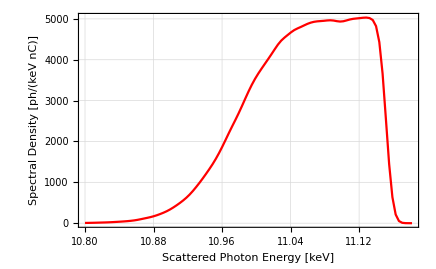

```mathematica
SpecPlot=ListLinePlot[SpecDen⟦2⟧,Frame->True,LabelStyle->{14,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->Which[(range/.trialcase)=="keV",{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},(range/.trialcase)=="MeV",{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"}],PlotStyle->Red,PlotRange->Full]
```

## Spectral Density Per Electron

```mathematica
SpecDenElectron=Partition[Riffle[SpecDen⟦2⟧⟦All,1⟧,(SpecDen⟦2⟧⟦All,2⟧)/Which[(range/.trialcase)=="keV",phkeVnC,(range/.trialcase)=="MeV",phMeVnC]],2];
```

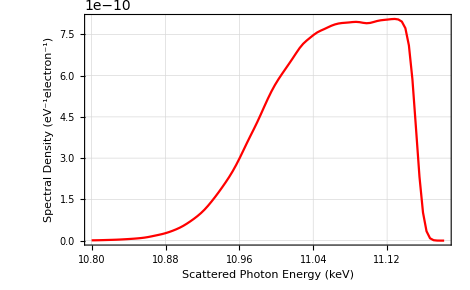

```mathematica
SpecElecPlot=ListLinePlot[SpecDenElectron,Frame->True,LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->Which[(range/.trialcase)=="keV",{"Scattered Photon Energy (keV)","Spectral Density (eV^-1electron^-1)"},(range/.trialcase)=="MeV",{"Scattered Photon Energy (MeV)","Spectral Density (eV^-1electron^-1)"}],PlotStyle->Red,PlotRange->Full]
```

## Normalised Intensity Plot

```mathematica
NormSpecDen=Partition[Riffle[SpecDen⟦2,All,1⟧,SpecDen⟦2,All,2⟧/Max[SpecDen⟦2,All,2⟧]],2];
```

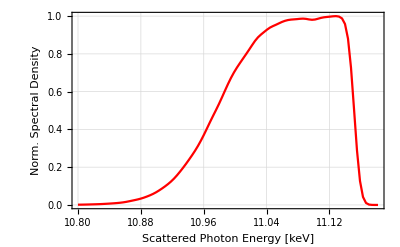

```mathematica
NormSpecPlot=ListLinePlot[NormSpecDen,Frame->True,LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->Which[(range/.trialcase)=="keV",{"Scattered Photon Energy [keV]","Norm. Spectral Density"},(range/.trialcase)=="MeV",{"Scattered Photon Energy [MeV]","Norm. Spectral Density"}],PlotStyle->Red,PlotRange->Full]
```

## Spectral Yield

```mathematica
SpectralYield=Integrate[Interpolation[SpecDen⟦2⟧][x],{x,Min[SpecDen⟦2,All,1⟧],Max[SpecDen⟦2,All,1⟧]}]*(Q/.trialcase)/nC
```

8.93952

## Saving

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseC/Case_C_lower"];
SpecDen>>"CASE_C_reduced_QMC_100M.txt";
NormSpecDen>>"CASE_C_reduced_NORM_QMC_100M.txt";
SpecDenElectron>>"CASE_C_reduced_e-_QMC_100M.txt";
ICARUSsummary>>"CASE_C_reduced_QMC_100M_SET.txt";
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseC/Case_C_lower"];
Export["CASE_C_reduced_QMC_100M_PLOT.pdf",SpecPlot];
```

## Comparison of New Results

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA_POL_TEST"];
CBETA150LINHORPOL=<<"CBETA150_0.5_RMS_QMC_20M_TAU_0.txt";
CBETA150LINVERPOL=<<"CBETA150_0.5_RMS_QMC_20M_TAU_PI2.txt";
```

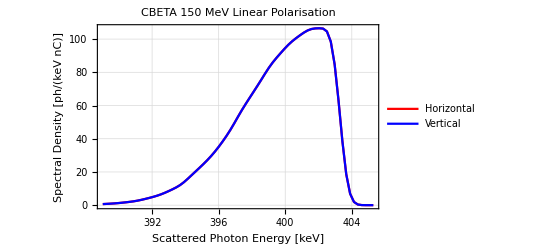

```mathematica
LinearPolComp=ListLinePlot[{CBETA150LINHORPOL⟦2⟧,CBETA150LINVERPOL⟦2⟧},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},PlotLabel->"CBETA 150 MeV Linear Polarisation",PlotLegends->Placed[LineLegend[{"Horizontal","Vertical"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->Full]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA_POL_TEST/FINAL_PLOTS"];
Export["CBETA150_0.5_RMS_QMC_20M_LinPol_PLOT.pdf",LinearPolComp];
```

## Comparison of Old Results

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/SUN2D_results/Polarisation"];
CBETAOLDPI2=<<"CBETA150_piby2_100M.txt";
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/SUN2D_results/no_integration_points_bench"];
CBETA150OLD0=<<"CBETA150_200mil.txt";
```

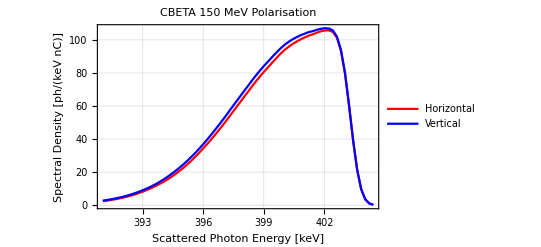

```mathematica
OldPolComp=ListLinePlot[{CBETA150OLD0,CBETAOLDPI2},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},PlotLabel->"CBETA 150 MeV Polarisation",PlotLegends->Placed[LineLegend[{"Horizontal","Vertical"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->Full]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA_POL_TEST/FINAL_PLOTS"];
Export["CBETA150_OLD_POL_COMP_PLOT.pdf",OldPolComp];
```

## Comparison of Old and New Linear Polarisation

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA_POL_TEST"];
CBETA150NEWLIN=<<"CBETA150_0.5_RMS_QMC_100M_TAU_PI0.txt";
```

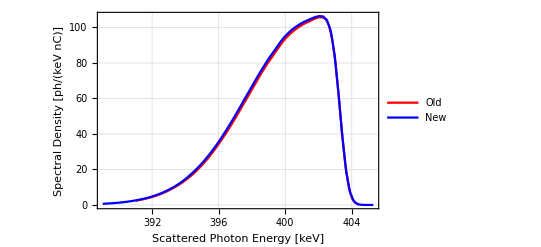

```mathematica
PolComp=ListLinePlot[{CBETA150OLD0,CBETA150NEWLIN⟦2⟧},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"}(*,PlotLabel->"CBETA 150 MeV Polarisation"*),PlotLegends->Placed[LineLegend[{"Old","New"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->Full]
```

## Comparison with ICCS3D

```mathematica
rawdata=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA/CBETA150_RMS_ICCS3D_FINAL.txt","Words"];
ndata=Length[rawdata];
ncolumns=6;
ndat=ndata/ncolumns;
BalsaICCS=Array[Ω,{2,ndat}];
For[i=0,i<(ndat+1),i++,
(*for energy*)
Ω[1,i]=Interpreter["Number"][ToString[rawdata⟦1+ncolumns*(i-1)⟧]]*10^-3;
(*for specden*)
Ω[2,i]=Interpreter["Number"][ToString[rawdata⟦3+ncolumns*(i-1)⟧]]*phkeVnC;
];
BalsaVals=Array[Υ,{2,0}];
For[i=1,i<Length[Transpose[BalsaICCS]]+1,i++,
If[BalsaICCS⟦2,i⟧>10^-30,
AppendTo[BalsaVals⟦1⟧,BalsaICCS⟦1,i⟧];
AppendTo[BalsaVals⟦2⟧,BalsaICCS⟦2,i⟧];
];
];
```

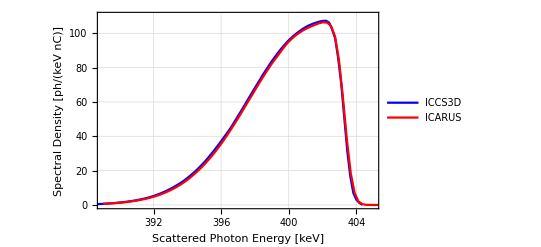

```mathematica
ListLinePlot[{Transpose[BalsaVals],CBETA150NEWLIN⟦2⟧},Frame->True,PlotStyle->{Blue,Red},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},PlotLegends->Placed[LineLegend[{"ICCS3D","ICARUS"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{389,405},{0,110}}]
```

## Thesis Cases + ICCS3D Comparison

### Case A

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseA"];
CaseAdat=<<"CASE_A_QMC_100M.txt";
```

```mathematica
rawdataA=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/ICCS3D_OUTPUT_FIXED/A/long/output_ICCS3D.txt","Table"];
```

```mathematica
caseAminval=Min[CaseAdat⟦2,All,1⟧];
caseAmaxval=Max[CaseAdat⟦2,All,1⟧];
```

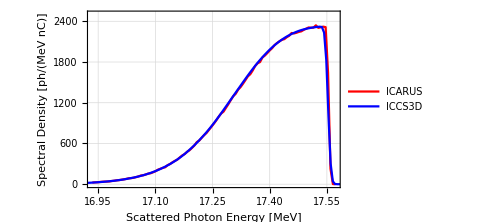

```mathematica
CaseAplot=ListLinePlot[{CaseAdat⟦2⟧,Partition[Riffle[1.001*rawdataA⟦All,1⟧/MeV,rawdataA⟦All,3⟧*phMeVnC*10],2]},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{caseAminval,caseAmaxval},{0,2500}},ImageSize->Medium]
```

### Case B

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseB"];
CaseBdat=<<"CASE_B_QMC_150M.txt";
```

```mathematica
rawdataB=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/ICCS3D_OUTPUT_FIXED/B/long/output_ICCS3D.txt","Table"];
```

```mathematica
caseBminval=Min[CaseBdat⟦2,All,1⟧];
caseBmaxval=Max[CaseBdat⟦2,All,1⟧];
```

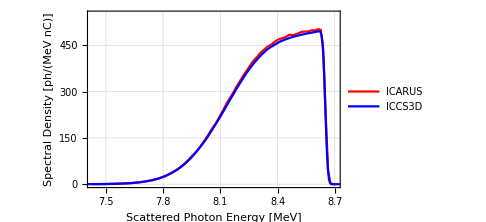

```mathematica
CaseBplot=ListLinePlot[{CaseBdat⟦2⟧,Partition[Riffle[1.0015*rawdataB⟦All,1⟧/MeV,rawdataB⟦All,3⟧*phMeVnC*10],2]},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{caseBminval,caseBmaxval},{0,550}},ImageSize->Medium]
```

### Case C

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseC"];
CaseCdat=<<"CASE_C_QMC_100M.txt";
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseC/Case_C_lower"];
CaseCreduced=<<"CASE_C_reduced_QMC_100M.txt";
```

```mathematica
rawdataC=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/ICCS3D_OUTPUT_FIXED/C/long/output_ICCS3D.txt","Table"];
```

```mathematica
rerunC=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/ICCS3D_OUTPUT_FIXED/C/long/output_ICCS3D_caseC_rerun.txt","Table"];
```

```mathematica
caseCminval=Min[CaseCdat⟦2,All,1⟧];
caseCmaxval=Max[CaseCdat⟦2,All,1⟧];
```

The smaller than 10 factor applied to scale ICCS3D and the energy scaling are due to the energy being different in Balsa’s simulations.

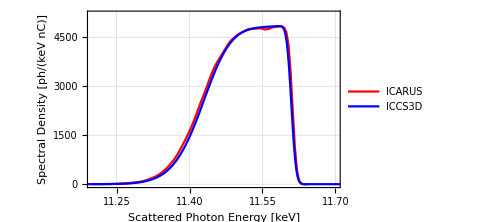

```mathematica
CaseCplot=ListLinePlot[{CaseCdat⟦2⟧,Partition[1.0414*Riffle[rerunC⟦All,1⟧/keV,rerunC⟦All,3⟧*phkeVnC*9.25],2]},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.23,0.7}],PlotRange->{{11.2,11.7},{0,5200}},ImageSize->Medium]
```

### Grid

```mathematica
Casesplot=Grid[{{CaseAplot,CaseBplot},{CaseCplot}}]
```

-Graphics- | -Graphics-
-Graphics- |